# Rollups benchmarks

## Benchmarking exec units as a function of “update length”

## Preamble

```mathematica
SetDirectory[NotebookDirectory[]];
```

#### Reference protocol parameters (June 2023)

```mathematica
maxExSteps=10000000000;
maxExMem=14000000;
```

#### Import benchmark data

```mathematica
data=Import["rollupBench_1.csv","CSV"];
```

## Data analysis

### CPU

```mathematica
cpuData={#⟦1⟧,#⟦2⟧}&/@data
```

{{0,3932911529},{1,3951536557},{3,4010872807},{5,4108149099},{10,4501571619},{15,5116254439},{20,5949205309},{25,7000133379},{30,8275563299},{35,9766185919},{40,11477861089},{45,13410838109},{50,15562332479}}

#### Data plot (CPU)

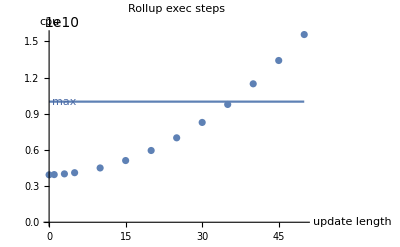

```mathematica
ListPlot[cpuData,PlotRange->All,
PlotLabel->"Rollup exec steps",AxesLabel->{"update length","cpu"}];
Plot[maxExSteps,{x,0,50}];
Graphics[Text[Style["max",RGBColor[0.297856, 0.423621, 0.656168]],{3,maxExSteps},{0,-1}]];
cpuPlot=Show[%%%,%%,%]
```

#### Reaching maximum budget

```mathematica
FindRoot[Interpolation[cpuData][ul]==maxExSteps,{ul,40}]
```

{ul→35.7229}

∴ CPU budget is exceded when update length is ≥ 36 .

### Memory

```mathematica
memData={#⟦1⟧,#⟦3⟧}&/@data
```

{{0,1342318},{1,1383725},{3,1488795},{5,1676873},{10,2410228},{15,3562383},{20,5113338},{25,7063093},{30,9451648},{35,12219003},{40,15405158},{45,19010113},{50,23013868}}

#### Data plot (memory)

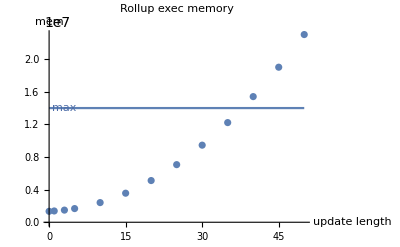

```mathematica
ListPlot[memData,PlotRange->All,
PlotLabel->"Rollup exec memory",AxesLabel->{"update length","mem"}];
Plot[maxExMem,{x,0,50}];
Graphics[Text[Style["max",RGBColor[0.297856, 0.423621, 0.656168]],{3,maxExMem},{0,-1}]];
memPlot=Show[%%%,%%,%]
```

#### Reaching maximum budget

```mathematica
FindRoot[Interpolation[memData][ul]==maxExMem,{ul,40}]
```

{ul→37.8752}

∴ Memory budget is exceded when update length is ≥ 38 .

## Conclusion

To be within exec units budget, update length must be 35 or less.

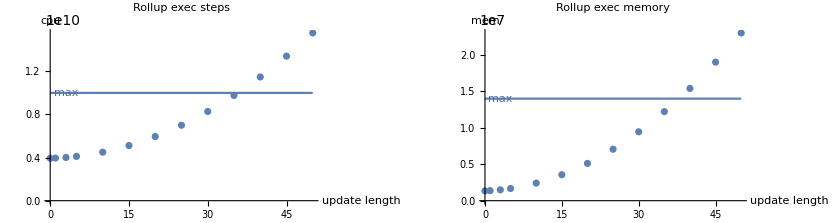

```mathematica
GraphicsRow[{cpuPlot,memPlot}]
```